```mathematica
Quit[]
```

## Load Packages

```mathematica
$LoadFeynArts=True;
Global`$LoadAddOns={"FeynHelpers"};
<<FeynCalc`;
$FAVerbose = 0;

FAPatch[PatchModelsOnly->True];
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.1 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

FeynHelpers 1.1.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

Patching FeynArts models... done!

## Diagram and amplitude utilities

### Functions for generating diagrams

```mathematica
exclusions={V[1],V[2]};

frModelName="EFT_MeV_DM_scalar";
model={frModelName<>"/"<>frModelName};
genericModel={"Lorentz",frModelName<>"/"<>frModelName};

insertionLevel={Particles};
```

```mathematica
genDiags[inFields_,outFields_,nLoops_:0,adj_:{3,4,5},otherExclusions_:{}]:=Block[{tops},
tops=CreateTopologies[nLoops, Length[inFields]-> Length[outFields],ExcludeTopologies-> {Tadpoles,SelfEnergies,WFCorrections},Adjacencies-> adj];
InsertFields[tops,inFields-> outFields,InsertionLevel-> insertionLevel,Model-> model,GenericModel-> genericModel,ExcludeParticles-> Join[exclusions,otherExclusions]]
]
```

### Abbreviations for states

```mathematica
stateπ0=S[1];
stateπm=S[2];
stateπp=-S[2];
statek0=S[3];
statek0bar=-S[3];
statekm=S[4];
statekp=-S[4];
stateη=S[5];
stateγ=V[1];
stateρ=V[2];
stateν=F[1];
stateνbar=-F[1];
statel=F[2];
statelbar=-F[2];
statex=F[3];
statexbar=-F[3];
states=S[7];

mesonList={stateπ0,stateπp,stateπm,statekp,statekm,statek0,statek0bar,stateη};
```

### Three body phase space bounds

```mathematica
getTBounds[s_,m1_,m2_,m3_,M_]:=Module[{E1,E2,t,BoundsLHS,BoundsRHS,solns,holdassumptions},
holdassumptions=$Assumptions;
$Assumptions=Join[$Assumptions,{getSBounds⟦1⟧<s<getSBounds⟦2⟧}];
(* energies *)
E1=  (M^2+m1^2-s)/(2M);
E2= (M^2+m2^2-t)/(2M);
(* LHS boundary equation *)
BoundsLHS=(M^2+2E1 E2 +m1^2+m2^2-m3^2-2M(E1+E2))//Simplify;
(* RHS boundary equation *)
BoundsRHS=(2 √((E1^2-m1^2)(E2^2-m2^2)))//FullSimplify;
(* solution to boundary equation *)
solns=Simplify[Solve[BoundsLHS==BoundsRHS,t]];
$Assumptions=holdassumptions;
{solns⟦2⟧⟦1⟧⟦2⟧,solns⟦1⟧⟦1⟧⟦2⟧}
]

getSBounds[m1_,m2_,m3_,M_]:={(m2+m3)^2,(M-m1)^2};


getYBounds[x_,m1_,m2_,m3_,M_]:=Module[{E1,E2,y,BoundsLHS,BoundsRHS,solns,holdassumptions},
holdassumptions=$Assumptions;
$Assumptions=Join[$Assumptions,{getXBounds⟦1⟧<x<getXBounds⟦2⟧}];
(* energies *)
E1=  M x/ 2;
E2= M y/ 2;
(* LHS boundary equation *)
BoundsLHS=(M^2+2E1 E2 +m1^2+m2^2-m3^2-2M(E1+E2))//Simplify;
(* RHS boundary equation *)
BoundsRHS=(2 √((E1^2-m1^2)(E2^2-m2^2)))//FullSimplify;
(* solution to boundary equation *)
solns=Simplify[Solve[BoundsLHS==BoundsRHS,y]];
$Assumptions=holdassumptions;
{solns⟦2⟧⟦1⟧⟦2⟧,solns⟦1⟧⟦1⟧⟦2⟧}]


getXBounds[m1_,m2_,m3_,M_]:={(M^2-(M-m1)^2+m1^2)/M^2,(M^2-(m2+m3)^2+m1^2)/M^2};
```

## S→ π^+π^-

### Compute Matrix Element

```mathematica
ClearScalarProducts[]
```

Null[]

```mathematica
SP[pπp,pπp]=(μπ*ms)^2;
SP[pπm,pπm]=(μπ*ms)^2;
SP[k,k]=0;

SP[pπp,pπm]=1/2(ms^2-(μπ*ms)^2-(μπ*ms)^2);
```

```mathematica
Module[{diags,ampFA,ampFC,amp,ampConj,msqrd},
diags=genDiags[{states},{stateπp,stateπm}];

ampFA=CreateFeynAmp[diags];

ampFC=FCFAConvert[ampFA,
IncomingMomenta-> {ps},
OutgoingMomenta-> {pπp,pπm},
List-> False,
UndoChiralSplittings-> True,
LorentzIndexNames-> {μ,ν,ρ,σ},
ChangeDimension-> 4,
FinalSubstitutions-> M$FACouplings];

amp=ampFC//PropagatorDenominatorExplicit//Contract//ReplaceAll[#,{mpi-> μπ*ms,contactRhoSCoeff-> 0,muq-> b0/(μπ*ms)^2-mdq}]&;
ampConj=ComplexConjugate[amp]//ReplaceAll[#,{μ-> α,ν-> β,ρ-> λ,σ-> ζ}]&;
msqrd = amp*ampConj//FermionSpinSum//ReplaceAll[#,DiracTrace-> Tr]&;
msqrd = msqrd//DoPolarizationSums[#,k,0]&//Simplify;
sπpπm`msqrd=msqrd]
```

(2 (b0^2 (4 gsGG vs+9 vh) (9 gsff (16 gsGG vs+9 vh)-32 gsGG^2 vs+54 gsGG vh)-54 gsGG μπ^2 (2 μπ^2-1) ms^4 vh (3 gsff vs+2 gsGG vs+3 vh))^2)/(729 μπ^4 ms^4 vh^2 (4 gsGG vs+9 vh)^2 (3 gsff vs+2 gsGG vs+3 vh)^2)

```mathematica
sπpπm`Γ=1/(2ms)(4π)/(16 π^2)((√(1-4 μπ^2))/2)sπpπm`msqrd//FullSimplify
```

(√(1-4 μπ^2) (b0^2 (4 gsGG vs+9 vh) (27 vh (3 gsff+2 gsGG)+16 gsGG vs (9 gsff-2 gsGG))+54 gsGG μπ^2 (1-2 μπ^2) ms^4 vh (3 gsff vs+2 gsGG vs+3 vh))^2)/(5832 π μπ^4 ms^5 vh^2 (4 gsGG vs+9 vh)^2 (3 gsff vs+2 gsGG vs+3 vh)^2)

## S→ π^+π^- γ

### Compute Matrix element

```mathematica
ClearScalarProducts[]
```

Null[]

```mathematica
SP[pπp,pπp]=(μπ*ms)^2;
SP[pπm,pπm]=(μπ*ms)^2;
SP[k,k]=0;

SP[pπp,pπm]=1/2(s-(μπ*ms)^2-(μπ*ms)^2);
SP[k,pπm]=1/2(t-0-(μπ*ms)^2);
SP[k,pπp]=1/2(u-0-(μπ*ms)^2);
```

```mathematica
Module[{diags,ampFA,ampFC,amp,ampConj,msqrd},
diags=genDiags[{states},{stateπp,stateπm,stateγ}];

ampFA=CreateFeynAmp[diags];

ampFC=FCFAConvert[ampFA,
IncomingMomenta-> {ps},
OutgoingMomenta-> {pπp,pπm,k},
List-> False,
UndoChiralSplittings-> True,
LorentzIndexNames-> {μ,ν,ρ,σ},
ChangeDimension-> 4,
FinalSubstitutions-> M$FACouplings];

amp=ampFC//PropagatorDenominatorExplicit//Contract//ReplaceAll[#,{mpi-> μπ*ms,contactRhoSCoeff-> 0,muq-> b0/(μπ*ms)^2-mdq}]&;
ampConj=ComplexConjugate[amp]//ReplaceAll[#,{μ-> α,ν-> β,ρ-> λ,σ-> ζ}]&;
msqrd = amp*ampConj//FermionSpinSum//ReplaceAll[#,DiracTrace-> Tr]&;
msqrd = msqrd//DoPolarizationSums[#,k,0]&//Simplify;
sπpπmγ`msqrd=msqrd]
```

-(4 qe^2 (s (t-μπ^2 ms^2) (μπ^2 ms^2-u)+μπ^2 ms^2 (-2 μπ^2 ms^2+t+u)^2) (b0^2 (4 gsGG vs+9 vh) (9 gsff (16 gsGG vs+9 vh)-32 gsGG^2 vs+54 gsGG vh)+54 gsGG μπ^2 ms^2 vh (3 gsff vs+2 gsGG vs+3 vh) (-4 μπ^2 ms^2+s+t+u))^2)/(729 μπ^4 ms^4 vh^2 (4 gsGG vs+9 vh)^2 (t-μπ^2 ms^2)^2 (u-μπ^2 ms^2)^2 (3 gsff vs+2 gsGG vs+3 vh)^2)

### Convert to x and y

```mathematica
sπpπmγ`dΓdsdt=(1/(2ms))(1/(16 ms^2(2π)^3))sπpπmγ`msqrd//ReplaceAll[#,u-> ms^2+2 ms^2 μπ^2-s-t]&//Simplify;
sπpπmγ`dΓdxdy=ms^4 sπpπmγ`dΓdsdt//ReplaceAll[#,{s-> ms^2(1-x),t-> ms^2(1-y+μπ^2)}]&//Simplify;
```

```mathematica
sπpπmγ`dΓdxdy`dynamic=sπpπmγ`dΓdxdy//SelectNotFree[#,y]&
sπpπmγ`dΓdxdy`coeff=sπpπmγ`dΓdxdy//SelectFree[#,y]&
```

(x^2 (-μπ^2+y-1)+x (y^2-3 y+2)-(y-1)^2)/((y-1)^2 (x+y-1)^2)

((b0^2 qe (4 gsGG vs+9 vh) (9 gsff (16 gsGG vs+9 vh)-32 gsGG^2 vs+54 gsGG vh)-54 gsGG μπ^2 (2 μπ^2-1) ms^4 qe vh (3 gsff vs+2 gsGG vs+3 vh))^2)/(46656 π^3 μπ^4 ms^5 vh^2 (4 gsGG vs+9 vh)^2 (3 gsff vs+2 gsGG vs+3 vh)^2)

### Compute y integral

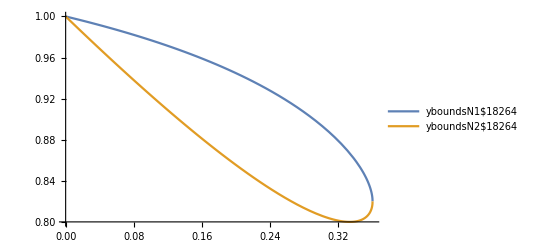

```mathematica
ybounds = getYBounds[x,0,μπ*ms,μπ*ms,ms]//Simplify;
xbounds=getXBounds[0,μπ*ms,μπ*ms,ms]//Simplify;

Module[{yboundsN1,yboundsN2,xboundsN1,xboundsN2},
(* test which curve is the upper and which is lower *)
yboundsN1=ybounds⟦1⟧/.{μπ-> 0.4,ms->1};
yboundsN2=ybounds⟦2⟧/.{μπ-> 0.4,ms->1};
xboundsN1=xbounds⟦1⟧/.{μπ-> 0.4,ms->1};
xboundsN2=xbounds⟦2⟧/.{μπ-> 0.4,ms->1};
Plot[{yboundsN1,yboundsN2},{x,xboundsN1,xboundsN2},PlotLegends->"Expressions"]
]
```

```mathematica
Module[{integral,lim1,lim2,result},
$Assumptions={xbounds⟦1⟧<x<xbounds⟦2⟧,μl>0};
integral=Integrate[sπpπmγ`dΓdxdy`dynamic,y]//Simplify;
lim1=integral/.{y-> ybounds⟦1⟧};
lim2=integral/.{y-> ybounds⟦2⟧};
$Assumptions=True;
sπpπmγ`dΓdx`dynamic=lim1-lim2//Simplify
]
```

(2 √(x-1) √(4 μπ^2+x-1)+(2 μπ^2+x-1) log((x (-√(x-1) √(4 μπ^2+x-1)+x-1))/(2 (x-1)))+(2 μπ^2+x-1) log((x (√(x-1) √(4 μπ^2+x-1)-x+1))/(2 (x-1)))-(2 μπ^2+x-1) log(-(x (√(x-1) √(4 μπ^2+x-1)+x-1))/(2 (x-1)))-(2 μπ^2+x-1) log((x (√(x-1) √(4 μπ^2+x-1)+x-1))/(2 (x-1))))/x

```mathematica
sπpπmγ`dΓdx`dynamic//SelectNotFree[#,Log[__]]&//SelectNotFree[#,Log[__]]&//StandardForm
```

(-1+x+2 μπ^2) Log[(x (-1+x-√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))]+(-1+x+2 μπ^2) Log[(x (1-x+√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))]-(-1+x+2 μπ^2) Log[-(x (-1+x+√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))]-(-1+x+2 μπ^2) Log[(x (-1+x+√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))]

```mathematica
sπpπmγ`dΓdx`dynamic//StandardForm
```

(2 √(-1+x) √(-1+x+4 μπ^2)+(-1+x+2 μπ^2) Log[(x (-1+x-√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))]+(-1+x+2 μπ^2) Log[(x (1-x+√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))]-(-1+x+2 μπ^2) Log[-(x (-1+x+√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))]-(-1+x+2 μπ^2) Log[(x (-1+x+√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))])/x

Simply logs by hand

```mathematica
(-1+x+2 μπ^2) Log[(x (-1+x-√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))]
+(-1+x+2 μπ^2) Log[(x (1-x+√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))]
-(-1+x+2 μπ^2) Log[-(x (-1+x+√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))]
-(-1+x+2 μπ^2) Log[(x (-1+x+√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))]
```

```mathematica
(((x (-1+x-√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x)))/1)(((x (1-x+√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x)))/1)(1/(-(x (-1+x+√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))))(1/((x (-1+x+√(-1+x) √(-1+x+4 μπ^2)))/(2 (-1+x))))//Simplify//StandardForm
```

((1-x+√(-1+x) √(-1+x+4 μπ^2))^2)/((-1+x+√(-1+x) √(-1+x+4 μπ^2))^2)

Compute put logs back in

```mathematica
sπpπmγ`dΓdx`dynamic=1/x(2 √(-1+x) √(-1+x+4 μπ^2)+(-1+x+2 μπ^2) Log[((1-x+√(-1+x) √(-1+x+4 μπ^2))^2)/((-1+x+√(-1+x) √(-1+x+4 μπ^2))^2)])
```

(2 √(x-1) √(4 μπ^2+x-1)+(2 μπ^2+x-1) log(((√(x-1) √(4 μπ^2+x-1)-x+1)^2)/((√(x-1) √(4 μπ^2+x-1)+x-1)^2)))/x

```mathematica
sπpπmγ`dΓdx`dynamic/.{μπ-> 0.1,x-> 0.5}
```

5.51354+0. ⅈ

### Compute Spectrum

```mathematica
sπpπmγ`dndx=sπpπmγ`dΓdx`dynamic*sπpπmγ`dΓdxdy`coeff/sπpπm`Γ//Simplify
```

(qe^2 (2 √(x-1) √(4 μπ^2+x-1)+(2 μπ^2+x-1) log(((√(x-1) √(4 μπ^2+x-1)-x+1)^2)/((√(x-1) √(4 μπ^2+x-1)+x-1)^2))))/(8 π^2 √(1-4 μπ^2) x)

```mathematica
sπpπmγ`dΓdx`dynamic/.{μπ-> mupi}//FortranForm
```

(2*Sqrt(-1 + x)*Sqrt(-1 + 4*mupi**2 + x) + (-1 + 2*mupi**2 + x)*Log((1 - x + Sqrt(-1 + x)*Sqrt(-1 + 4*mupi**2 + x))**2/(-1 + x + Sqrt(-1 + x)*Sqrt(-1 + 4*mupi**2 + x))**2))/x

```mathematica
FullSimplify[(sπpπmγ`dΓdxdy`coeff/sπpπm`Γ)]/.{μπ-> mupi}//FortranForm
```

qe**2/(8.*Sqrt(1 - 4*mupi**2)*Pi**2)

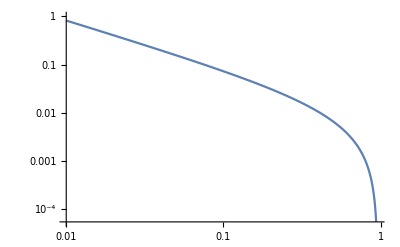

```mathematica
LogLogPlot[sπpπmγ`dndx/.{μπ-> 0.1,qe-> (4Pi/137.)^(1/2)},{x,0.01,xbounds⟦2⟧/.{μπ-> 0.1} }]
```